### Estimation parameters

```mathematica
capN=50
m=8
```

50

8

```mathematica
6
```

6

### Recursion for the coefficients of the integer valued polynomials

```mathematica
q[0]:=1;
q[s_]:=Product[x-k,{k,1,s}]/Factorial[s];
```

```mathematica
q[0,0]:=1;
q[0,m_]:=0;
q[s_,k_]:=q[s-1,k-1]/s- q[s-1,k];
```

```mathematica
q[0,0]
q[0,10]
q[0,-1]
q[4,-1]
Table[q[s,k],{s,0,5},{k,0,5}] //MatrixForm
Expand[q[0]]
Expand[q[1]]
Expand[q[2]]
Expand[q[3]]
Expand[q[4]]
Expand[q[5]]
```

1

0

0

0

(1 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0
1 | -3/2 | 1/2 | 0 | 0 | 0
-1 | 11/6 | -1 | 1/6 | 0 | 0
1 | -25/12 | 35/24 | -5/12 | 1/24 | 0
-1 | 137/60 | -15/8 | 17/24 | -1/8 | 1/120)

1

-1+x

1-(3 x)/2+x^2/2

-1+(11 x)/6-x^2+x^3/6

1-(25 x)/12+(35 x^2)/24-(5 x^3)/12+x^4/24

-1+(137 x)/60-(15 x^2)/8+(17 x^3)/24-x^4/8+x^5/120

### Coefficient of the discrete orthogonal polynomials

```mathematica
d[k_]:=Factorial[k]/Binomial[2*k,k]*Sum[(-1)^(s+k)*Binomial[s+k,s]*Binomial[capN-s-1,capN-k-1]*q[s],{s,0,k}]
P[k_,i_]:=Factorial[k]/Binomial[2*k,k]*Sum[(-1)^(s+k)*Binomial[s+k,s]*Binomial[capN-s-1,capN-k-1]*q[s,i],{s,0,k}];
```

```mathematica
Table[P[k,i],{k,0,5},{i,0,5}] //MatrixForm
Expand[d[0]]
Expand[d[1]]
Expand[d[2]]
Expand[d[3]]
Expand[d[4]]
Expand[d[5]]
```

(1 | 0 | 0 | 0 | 0 | 0
-51/2 | 1 | 0 | 0 | 0 | 0
442 | -51 | 1 | 0 | 0 | 0
-35139/5 | 15761/10 | -153/2 | 1 | 0 | 0
3795012/35 | -273360/7 | 23567/7 | -102 | 1 | 0
-11595870/7 | 5989668/7 | -225675/2 | 5810 | -255/2 | 1)

1

-51/2+x

442-51 x+x^2

-35139/5+(15761 x)/10-(153 x^2)/2+x^3

3795012/35-(273360 x)/7+(23567 x^2)/7-102 x^3+x^4

-11595870/7+(5989668 x)/7-(225675 x^2)/2+5810 x^3-(255 x^4)/2+x^5

### Cramer-Rao bounds

```mathematica
CRB[i_,snr_]:=Sum[Factorial[k]^(-2)*Binomial[2*k,k]*P[k,i]^2/Binomial[capN+k,2*k+1],{k,0,m}]/(2*snr);
ApproxCRB[i_,snr_]:=1/(2*capN^(2*i+1)*snr)*(1/(2*i+1)+(m+1)^2/(2*capN*(i+1)^2)-1/(2*capN))*((m+i+1)*Binomial[m+i,i]*Binomial[m,i])^2;
```

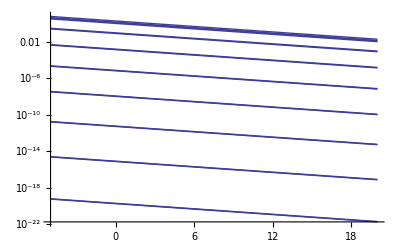

```mathematica
LogPlot[Flatten[Table[{CRB[i,10^(snrdb/10)],ApproxCRB[i,10^(snrdb/10)]},{i,0,m}]],{snrdb,-5,20}]
```

```mathematica
Table[{CRB[2,10^(snrdb/10)],ApproxCRB[2,10^(snrdb/10)]},{snrdb,-5,20}]
```

{{180154486291142265029/(179230650889352444928 √10),3361743/(3906250 √10)},{180154486291142265029/(179230650889352444928 10^(3/5)),3361743/(3906250 10^(3/5))},{180154486291142265029/(179230650889352444928 10^(7/10)),3361743/(3906250 10^(7/10))},{180154486291142265029/(179230650889352444928 10^(4/5)),3361743/(3906250 10^(4/5))},{180154486291142265029/(179230650889352444928 10^(9/10)),3361743/(3906250 10^(9/10))},{180154486291142265029/1792306508893524449280,3361743/39062500},{180154486291142265029/(1792306508893524449280 10^(1/10)),3361743/(39062500 10^(1/10))},{180154486291142265029/(1792306508893524449280 10^(1/5)),3361743/(39062500 10^(1/5))},{180154486291142265029/(1792306508893524449280 10^(3/10)),3361743/(39062500 10^(3/10))},{180154486291142265029/(1792306508893524449280 10^(2/5)),3361743/(39062500 10^(2/5))},{180154486291142265029/(1792306508893524449280 √10),3361743/(39062500 √10)},{180154486291142265029/(1792306508893524449280 10^(3/5)),3361743/(39062500 10^(3/5))},{180154486291142265029/(1792306508893524449280 10^(7/10)),3361743/(39062500 10^(7/10))},{180154486291142265029/(1792306508893524449280 10^(4/5)),3361743/(39062500 10^(4/5))},{180154486291142265029/(1792306508893524449280 10^(9/10)),3361743/(39062500 10^(9/10))},{180154486291142265029/17923065088935244492800,3361743/390625000},{180154486291142265029/(17923065088935244492800 10^(1/10)),3361743/(390625000 10^(1/10))},{180154486291142265029/(17923065088935244492800 10^(1/5)),3361743/(390625000 10^(1/5))},{180154486291142265029/(17923065088935244492800 10^(3/10)),3361743/(390625000 10^(3/10))},{180154486291142265029/(17923065088935244492800 10^(2/5)),3361743/(390625000 10^(2/5))},{180154486291142265029/(17923065088935244492800 √10),3361743/(390625000 √10)},{180154486291142265029/(17923065088935244492800 10^(3/5)),3361743/(390625000 10^(3/5))},{180154486291142265029/(17923065088935244492800 10^(7/10)),3361743/(390625000 10^(7/10))},{180154486291142265029/(17923065088935244492800 10^(4/5)),3361743/(390625000 10^(4/5))},{180154486291142265029/(17923065088935244492800 10^(9/10)),3361743/(390625000 10^(9/10))},{180154486291142265029/179230650889352444928000,3361743/3906250000}}

Plot the CRBs to a file

```mathematica
ToMetaPostString[v_] := ToString[NumberForm[v,ExponentFunction->(1 Quotient[#,1]&),NumberFormat->(Row[{#1,"e",#3}]&)]];Do[fname = FileNameJoin[{Directory[],"/Software/pubtex/polyphase_estimation/crbs/code/crbN" <> ToString[capN] <> "m" <> ToString[m] <> "i" <> ToString[i]}];
str = OpenWrite[fname];
Do[WriteString[str, ToMetaPostString[N[snrdb]] <> "\t"  <> ToMetaPostString[N[CRB[i,10^(snrdb/10)]]]  "\n"],{snrdb,-5,25}];
Close[str];
,{i,0,m}]
```

OpenWrite::noopen: Cannot open "/home/harprobey/Software/polynomialphasecrbs/code/Software/pubtex/polyphase_estimation/crbs/code/crbN50m8i0".

WriteString::strml: $Failed is not a string, stream, or list of strings and streams.

General::stop: Further output of WriteString :: strml will be suppressed during this calculation.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

OpenWrite::noopen: Cannot open "/home/harprobey/Software/polynomialphasecrbs/code/Software/pubtex/polyphase_estimation/crbs/code/crbN50m8i1".

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

OpenWrite::noopen: Cannot open "/home/harprobey/Software/polynomialphasecrbs/code/Software/pubtex/polyphase_estimation/crbs/code/crbN50m8i2".

General::stop: Further output of OpenWrite :: noopen will be suppressed during this calculation.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::stop: Further output of General :: stream will be suppressed during this calculation.

```mathematica
ToMetaPostString[v_] := ToString[NumberForm[v,ExponentFunction->(1 Quotient[#,1]&),NumberFormat->(Row[{#1,"e",#3}]&)]];Do[fname = FileNameJoin[{Directory[],"/Software/pubtex/polyphase_estimation/crbs/code/approxcrbN" <> ToString[capN] <> "m" <> ToString[m] <> "i" <> ToString[i]}];
str = OpenWrite[fname];
Do[WriteString[str, ToMetaPostString[N[snrdb]] <> "\t"  <> ToMetaPostString[N[ApproxCRB[i,10^(snrdb/10)]]]  "\n"],{snrdb,-5,25}];
Close[str];
,{i,0,m}]
```

OpenWrite::noopen: Cannot open "/home/harprobey/Software/polynomialphasecrbs/code/Software/pubtex/polyphase_estimation/crbs/code/approxcrbN50m8i0".

WriteString::strml: $Failed is not a string, stream, or list of strings and streams.

General::stop: Further output of WriteString :: strml will be suppressed during this calculation.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

OpenWrite::noopen: Cannot open "/home/harprobey/Software/polynomialphasecrbs/code/Software/pubtex/polyphase_estimation/crbs/code/approxcrbN50m8i1".

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

OpenWrite::noopen: Cannot open "/home/harprobey/Software/polynomialphasecrbs/code/Software/pubtex/polyphase_estimation/crbs/code/approxcrbN50m8i2".

General::stop: Further output of OpenWrite :: noopen will be suppressed during this calculation.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::stop: Further output of General :: stream will be suppressed during this calculation.